## This is for sanity checking - Spot check to verify the lines in the graphs correspond to the data

```mathematica
dataoutputfolder="/Users/chrisrichards/Desktop/FrogWork/CODE/mujoco150_KM/output/data_for_plots/momentarm/absoluteScaling";
(*"/Users/chrisrichards/Desktop/FrogWork/CODE/mujoco150_KM/output/data_for_plots/momentarm/relativeScaling";*)
plotsfolder="/Users/chrisrichards/Desktop/FrogWork/CODE/mujoco150_KM/output/plots/";
SetDirectory[dataoutputfolder];
datafiles=FileNames[];
ResetDirectory[];
SetDirectory[plotsfolder];
plotfiles=FileNames[];
ResetDirectory[];
Print["plot files..."]
ColumnForm[plotfiles]
Print["data files.."]
MatrixForm[Thread[{Range[Length[datafiles]],datafiles}]]
```

plot files...

.DS_Store
Figure_HYP_axial_LatRotation_README.txt
Figure_HYP_axial_LatRotation_relativeScaling.png
Figure_HYP_misc_AA_README.txt
Figure_HYP_misc_AA_relativeScaling.png
Figure_HYP_misc_FE_README.txt
Figure_HYP_misc_FE_relativeScaling.png
Figure_HYP_misc_LAR_README.txt
Figure_HYP_misc_LAR_relativeScaling.png
Figure_HYP_pro_AA_README.txt
Figure_HYP_pro_AA_relativeScaling.png
Figure_HYP_pro_FE_README.txt
Figure_HYP_pro_FE_relativeScaling.png
Figure_HYP_pro_LAR_README.txt
Figure_HYP_pro_LAR_relativeScaling.png
Figure_HYP_pro&ret_AA_README.txt
Figure_HYP_pro&ret_AA_relativeScaling.png
Figure_HYP_pro&ret_FE_README.txt
Figure_HYP_pro&ret_FE_relativeScaling.png
Figure_HYP_pro&ret_LAR_README.txt
Figure_HYP_pro&ret_LAR_relativeScaling.png
Figure_HYP_ret_AA_README.txt
Figure_HYP_ret_AA_relativeScaling.png
Figure_HYP_ret_FE_README.txt
Figure_HYP_ret_FE_relativeScaling.png
Figure_HYP_ret_LAR_README.txt
Figure_HYP_ret_LAR_relativeScaling.png
Figure_RUN_axial_LatRotation_relativeScaling.png
Figure_RUN_misc_AA_relativeScaling.png
Figure_RUN_misc_FE_relativeScaling.png
Figure_RUN_misc_LAR_relativeScaling.png
Figure_RUN_pro_AA_relativeScaling.png
Figure_RUN_pro_FE_relativeScaling.png
Figure_RUN_pro_LAR_relativeScaling.png
Figure_RUN_pro&ret_AA_relativeScaling.png
Figure_RUN_pro&ret_FE_relativeScaling.png
Figure_RUN_pro&ret_LAR_relativeScaling.png
Figure_RUN_ret_AA_relativeScaling.png
Figure_RUN_ret_FE_relativeScaling.png
Figure_RUN_ret_LAR_relativeScaling.png
individual_plots
README_FIRST_obselete.txt
z_old_17.2.2021
z_old_19.4.2021
z_old_23.7.2021
z_old_24.5.21
z_old_26.1.21
z_old_29.1.2021

data files..

(1 | .DS_Store
2 | Figure_HYP_axial_LCIdist_ISY_fem10deg_ISXextended_LatRotation.csv
3 | Figure_HYP_axial_LCIdist_ISY_fem10deg_ISXfullFlexed_LatRotation.csv
4 | Figure_HYP_axial_LCIdist_ISY_fem10deg_ISXhalfFlexed_LatRotation.csv
5 | Figure_HYP_axial_LCImid_ISY_fem10deg_ISXextended_LatRotation.csv
6 | Figure_HYP_axial_LCImid_ISY_fem10deg_ISXfullFlexed_LatRotation.csv
7 | Figure_HYP_axial_LCImid_ISY_fem10deg_ISXhalfFlexed_LatRotation.csv
8 | Figure_HYP_axial_LCIprox_ISY_fem10deg_ISXextended_LatRotation.csv
9 | Figure_HYP_axial_LCIprox_ISY_fem10deg_ISXfullFlexed_LatRotation.csv
10 | Figure_HYP_axial_LCIprox_ISY_fem10deg_ISXhalfFlexed_LatRotation.csv
11 | Figure_HYP_axial_LIL0_ISY_fem10deg_ISXextended_LatRotation.csv
12 | Figure_HYP_axial_LIL0_ISY_fem10deg_ISXfullFlexed_LatRotation.csv
13 | Figure_HYP_axial_LIL0_ISY_fem10deg_ISXhalfFlexed_LatRotation.csv
14 | Figure_HYP_axial_LIL1_ISY_fem10deg_ISXextended_LatRotation.csv
15 | Figure_HYP_axial_LIL1_ISY_fem10deg_ISXfullFlexed_LatRotation.csv
16 | Figure_HYP_axial_LIL1_ISY_fem10deg_ISXhalfFlexed_LatRotation.csv
17 | Figure_HYP_axial_LIL2_ISY_fem10deg_ISXextended_LatRotation.csv
18 | Figure_HYP_axial_LIL2_ISY_fem10deg_ISXfullFlexed_LatRotation.csv
19 | Figure_HYP_axial_LIL2_ISY_fem10deg_ISXhalfFlexed_LatRotation.csv
20 | Figure_HYP_axial_LIL3_ISY_fem10deg_ISXextended_LatRotation.csv
21 | Figure_HYP_axial_LIL3_ISY_fem10deg_ISXfullFlexed_LatRotation.csv
22 | Figure_HYP_axial_LIL3_ISY_fem10deg_ISXhalfFlexed_LatRotation.csv
23 | Figure_HYP_axial_RCIdist_ISY_fem10deg_ISXextended_LatRotation.csv
24 | Figure_HYP_axial_RCIdist_ISY_fem10deg_ISXfullFlexed_LatRotation.csv
25 | Figure_HYP_axial_RCIdist_ISY_fem10deg_ISXhalfFlexed_LatRotation.csv
26 | Figure_HYP_axial_RCImid_ISY_fem10deg_ISXextended_LatRotation.csv
27 | Figure_HYP_axial_RCImid_ISY_fem10deg_ISXfullFlexed_LatRotation.csv
28 | Figure_HYP_axial_RCImid_ISY_fem10deg_ISXhalfFlexed_LatRotation.csv
29 | Figure_HYP_axial_RCIprox_ISY_fem10deg_ISXextended_LatRotation.csv
30 | Figure_HYP_axial_RCIprox_ISY_fem10deg_ISXfullFlexed_LatRotation.csv
31 | Figure_HYP_axial_RCIprox_ISY_fem10deg_ISXhalfFlexed_LatRotation.csv
32 | Figure_HYP_axial_RIL0_ISY_fem10deg_ISXextended_LatRotation.csv
33 | Figure_HYP_axial_RIL0_ISY_fem10deg_ISXfullFlexed_LatRotation.csv
34 | Figure_HYP_axial_RIL0_ISY_fem10deg_ISXhalfFlexed_LatRotation.csv
35 | Figure_HYP_axial_RIL1_ISY_fem10deg_ISXextended_LatRotation.csv
36 | Figure_HYP_axial_RIL1_ISY_fem10deg_ISXfullFlexed_LatRotation.csv
37 | Figure_HYP_axial_RIL1_ISY_fem10deg_ISXhalfFlexed_LatRotation.csv
38 | Figure_HYP_axial_RIL2_ISY_fem10deg_ISXextended_LatRotation.csv
39 | Figure_HYP_axial_RIL2_ISY_fem10deg_ISXfullFlexed_LatRotation.csv
40 | Figure_HYP_axial_RIL2_ISY_fem10deg_ISXhalfFlexed_LatRotation.csv
41 | Figure_HYP_axial_RIL3_ISY_fem10deg_ISXextended_LatRotation.csv
42 | Figure_HYP_axial_RIL3_ISY_fem10deg_ISXfullFlexed_LatRotation.csv
43 | Figure_HYP_axial_RIL3_ISY_fem10deg_ISXhalfFlexed_LatRotation.csv
44 | Figure_HYP_misc_LCR_hipL_fem10deg_ISXextended_AA.csv
45 | Figure_HYP_misc_LCR_hipL_fem10deg_ISXextended_FE.csv
46 | Figure_HYP_misc_LCR_hipL_fem10deg_ISXextended_LAR.csv
47 | Figure_HYP_misc_LCR_hipL_fem135deg_ISXextended_AA.csv
48 | Figure_HYP_misc_LCR_hipL_fem135deg_ISXextended_FE.csv
49 | Figure_HYP_misc_LCR_hipL_fem135deg_ISXextended_LAR.csv
50 | Figure_HYP_misc_LCR_hipL_fem45deg_ISXextended_AA.csv
51 | Figure_HYP_misc_LCR_hipL_fem45deg_ISXextended_FE.csv
52 | Figure_HYP_misc_LCR_hipL_fem45deg_ISXextended_LAR.csv
53 | Figure_HYP_misc_LCR_hipL_fem90deg_ISXextended_AA.csv
54 | Figure_HYP_misc_LCR_hipL_fem90deg_ISXextended_FE.csv
55 | Figure_HYP_misc_LCR_hipL_fem90deg_ISXextended_LAR.csv
56 | Figure_HYP_misc_LGL_hipL_fem10deg_ISXextended_AA.csv
57 | Figure_HYP_misc_LGL_hipL_fem10deg_ISXextended_FE.csv
58 | Figure_HYP_misc_LGL_hipL_fem10deg_ISXextended_LAR.csv
59 | Figure_HYP_misc_LGL_hipL_fem135deg_ISXextended_AA.csv
60 | Figure_HYP_misc_LGL_hipL_fem135deg_ISXextended_FE.csv
61 | Figure_HYP_misc_LGL_hipL_fem135deg_ISXextended_LAR.csv
62 | Figure_HYP_misc_LGL_hipL_fem45deg_ISXextended_AA.csv
63 | Figure_HYP_misc_LGL_hipL_fem45deg_ISXextended_FE.csv
64 | Figure_HYP_misc_LGL_hipL_fem45deg_ISXextended_LAR.csv
65 | Figure_HYP_misc_LGL_hipL_fem90deg_ISXextended_AA.csv
66 | Figure_HYP_misc_LGL_hipL_fem90deg_ISXextended_FE.csv
67 | Figure_HYP_misc_LGL_hipL_fem90deg_ISXextended_LAR.csv
68 | Figure_HYP_misc_LPY_hipL_fem10deg_ISXextended_AA.csv
69 | Figure_HYP_misc_LPY_hipL_fem10deg_ISXextended_FE.csv
70 | Figure_HYP_misc_LPY_hipL_fem10deg_ISXextended_LAR.csv
71 | Figure_HYP_misc_LPY_hipL_fem135deg_ISXextended_AA.csv
72 | Figure_HYP_misc_LPY_hipL_fem135deg_ISXextended_FE.csv
73 | Figure_HYP_misc_LPY_hipL_fem135deg_ISXextended_LAR.csv
74 | Figure_HYP_misc_LPY_hipL_fem45deg_ISXextended_AA.csv
75 | Figure_HYP_misc_LPY_hipL_fem45deg_ISXextended_FE.csv
76 | Figure_HYP_misc_LPY_hipL_fem45deg_ISXextended_LAR.csv
77 | Figure_HYP_misc_LPY_hipL_fem90deg_ISXextended_AA.csv
78 | Figure_HYP_misc_LPY_hipL_fem90deg_ISXextended_FE.csv
79 | Figure_HYP_misc_LPY_hipL_fem90deg_ISXextended_LAR.csv
80 | Figure_HYP_pro&ret_LAL_hipL_fem10deg_ISXextended_AA.csv
81 | Figure_HYP_pro&ret_LAL_hipL_fem10deg_ISXextended_FE.csv
82 | Figure_HYP_pro&ret_LAL_hipL_fem10deg_ISXextended_LAR.csv
83 | Figure_HYP_pro&ret_LAL_hipL_fem135deg_ISXextended_AA.csv
84 | Figure_HYP_pro&ret_LAL_hipL_fem135deg_ISXextended_FE.csv
85 | Figure_HYP_pro&ret_LAL_hipL_fem135deg_ISXextended_LAR.csv
86 | Figure_HYP_pro&ret_LAL_hipL_fem45deg_ISXextended_AA.csv
87 | Figure_HYP_pro&ret_LAL_hipL_fem45deg_ISXextended_FE.csv
88 | Figure_HYP_pro&ret_LAL_hipL_fem45deg_ISXextended_LAR.csv
89 | Figure_HYP_pro&ret_LAL_hipL_fem90deg_ISXextended_AA.csv
90 | Figure_HYP_pro&ret_LAL_hipL_fem90deg_ISXextended_FE.csv
91 | Figure_HYP_pro&ret_LAL_hipL_fem90deg_ISXextended_LAR.csv
92 | Figure_HYP_pro&ret_LAMcrv_hipL_fem10deg_ISXextended_AA.csv
93 | Figure_HYP_pro&ret_LAMcrv_hipL_fem10deg_ISXextended_FE.csv
94 | Figure_HYP_pro&ret_LAMcrv_hipL_fem10deg_ISXextended_LAR.csv
95 | Figure_HYP_pro&ret_LAMcrv_hipL_fem135deg_ISXextended_AA.csv
96 | Figure_HYP_pro&ret_LAMcrv_hipL_fem135deg_ISXextended_FE.csv
97 | Figure_HYP_pro&ret_LAMcrv_hipL_fem135deg_ISXextended_LAR.csv
98 | Figure_HYP_pro&ret_LAMcrv_hipL_fem45deg_ISXextended_AA.csv
99 | Figure_HYP_pro&ret_LAMcrv_hipL_fem45deg_ISXextended_FE.csv
100 | Figure_HYP_pro&ret_LAMcrv_hipL_fem45deg_ISXextended_LAR.csv
101 | Figure_HYP_pro&ret_LAMcrv_hipL_fem90deg_ISXextended_AA.csv
102 | Figure_HYP_pro&ret_LAMcrv_hipL_fem90deg_ISXextended_FE.csv
103 | Figure_HYP_pro&ret_LAMcrv_hipL_fem90deg_ISXextended_LAR.csv
104 | Figure_HYP_pro&ret_LAMstr_hipL_fem10deg_ISXextended_AA.csv
105 | Figure_HYP_pro&ret_LAMstr_hipL_fem10deg_ISXextended_FE.csv
106 | Figure_HYP_pro&ret_LAMstr_hipL_fem10deg_ISXextended_LAR.csv
107 | Figure_HYP_pro&ret_LAMstr_hipL_fem135deg_ISXextended_AA.csv
108 | Figure_HYP_pro&ret_LAMstr_hipL_fem135deg_ISXextended_FE.csv
109 | Figure_HYP_pro&ret_LAMstr_hipL_fem135deg_ISXextended_LAR.csv
110 | Figure_HYP_pro&ret_LAMstr_hipL_fem45deg_ISXextended_AA.csv
111 | Figure_HYP_pro&ret_LAMstr_hipL_fem45deg_ISXextended_FE.csv
112 | Figure_HYP_pro&ret_LAMstr_hipL_fem45deg_ISXextended_LAR.csv
113 | Figure_HYP_pro&ret_LAMstr_hipL_fem90deg_ISXextended_AA.csv
114 | Figure_HYP_pro&ret_LAMstr_hipL_fem90deg_ISXextended_FE.csv
115 | Figure_HYP_pro&ret_LAMstr_hipL_fem90deg_ISXextended_LAR.csv
116 | Figure_HYP_pro&ret_LGR_hipL_fem10deg_ISXextended_AA.csv
117 | Figure_HYP_pro&ret_LGR_hipL_fem10deg_ISXextended_FE.csv
118 | Figure_HYP_pro&ret_LGR_hipL_fem10deg_ISXextended_LAR.csv
119 | Figure_HYP_pro&ret_LGR_hipL_fem135deg_ISXextended_AA.csv
120 | Figure_HYP_pro&ret_LGR_hipL_fem135deg_ISXextended_FE.csv
121 | Figure_HYP_pro&ret_LGR_hipL_fem135deg_ISXextended_LAR.csv
122 | Figure_HYP_pro&ret_LGR_hipL_fem45deg_ISXextended_AA.csv
123 | Figure_HYP_pro&ret_LGR_hipL_fem45deg_ISXextended_FE.csv
124 | Figure_HYP_pro&ret_LGR_hipL_fem45deg_ISXextended_LAR.csv
125 | Figure_HYP_pro&ret_LGR_hipL_fem90deg_ISXextended_AA.csv
126 | Figure_HYP_pro&ret_LGR_hipL_fem90deg_ISXextended_FE.csv
127 | Figure_HYP_pro&ret_LGR_hipL_fem90deg_ISXextended_LAR.csv
128 | Figure_HYP_pro&ret_LIEdist_hipL_fem10deg_ISXextended_AA.csv
129 | Figure_HYP_pro&ret_LIEdist_hipL_fem10deg_ISXextended_FE.csv
130 | Figure_HYP_pro&ret_LIEdist_hipL_fem10deg_ISXextended_LAR.csv
131 | Figure_HYP_pro&ret_LIEdist_hipL_fem135deg_ISXextended_AA.csv
132 | Figure_HYP_pro&ret_LIEdist_hipL_fem135deg_ISXextended_FE.csv
133 | Figure_HYP_pro&ret_LIEdist_hipL_fem135deg_ISXextended_LAR.csv
134 | Figure_HYP_pro&ret_LIEdist_hipL_fem45deg_ISXextended_AA.csv
135 | Figure_HYP_pro&ret_LIEdist_hipL_fem45deg_ISXextended_FE.csv
136 | Figure_HYP_pro&ret_LIEdist_hipL_fem45deg_ISXextended_LAR.csv
137 | Figure_HYP_pro&ret_LIEdist_hipL_fem90deg_ISXextended_AA.csv
138 | Figure_HYP_pro&ret_LIEdist_hipL_fem90deg_ISXextended_FE.csv
139 | Figure_HYP_pro&ret_LIEdist_hipL_fem90deg_ISXextended_LAR.csv
140 | Figure_HYP_pro&ret_LIEprox_hipL_fem10deg_ISXextended_AA.csv
141 | Figure_HYP_pro&ret_LIEprox_hipL_fem10deg_ISXextended_FE.csv
142 | Figure_HYP_pro&ret_LIEprox_hipL_fem10deg_ISXextended_LAR.csv
143 | Figure_HYP_pro&ret_LIEprox_hipL_fem135deg_ISXextended_AA.csv
144 | Figure_HYP_pro&ret_LIEprox_hipL_fem135deg_ISXextended_FE.csv
145 | Figure_HYP_pro&ret_LIEprox_hipL_fem135deg_ISXextended_LAR.csv
146 | Figure_HYP_pro&ret_LIEprox_hipL_fem45deg_ISXextended_AA.csv
147 | Figure_HYP_pro&ret_LIEprox_hipL_fem45deg_ISXextended_FE.csv
148 | Figure_HYP_pro&ret_LIEprox_hipL_fem45deg_ISXextended_LAR.csv
149 | Figure_HYP_pro&ret_LIEprox_hipL_fem90deg_ISXextended_AA.csv
150 | Figure_HYP_pro&ret_LIEprox_hipL_fem90deg_ISXextended_FE.csv
151 | Figure_HYP_pro&ret_LIEprox_hipL_fem90deg_ISXextended_LAR.csv
152 | Figure_HYP_pro&ret_LIFB_hipL_fem10deg_ISXextended_AA.csv
153 | Figure_HYP_pro&ret_LIFB_hipL_fem10deg_ISXextended_FE.csv
154 | Figure_HYP_pro&ret_LIFB_hipL_fem10deg_ISXextended_LAR.csv
155 | Figure_HYP_pro&ret_LIFB_hipL_fem135deg_ISXextended_AA.csv
156 | Figure_HYP_pro&ret_LIFB_hipL_fem135deg_ISXextended_FE.csv
157 | Figure_HYP_pro&ret_LIFB_hipL_fem135deg_ISXextended_LAR.csv
158 | Figure_HYP_pro&ret_LIFB_hipL_fem45deg_ISXextended_AA.csv
159 | Figure_HYP_pro&ret_LIFB_hipL_fem45deg_ISXextended_FE.csv
160 | Figure_HYP_pro&ret_LIFB_hipL_fem45deg_ISXextended_LAR.csv
161 | Figure_HYP_pro&ret_LIFB_hipL_fem90deg_ISXextended_AA.csv
162 | Figure_HYP_pro&ret_LIFB_hipL_fem90deg_ISXextended_FE.csv
163 | Figure_HYP_pro&ret_LIFB_hipL_fem90deg_ISXextended_LAR.csv
164 | Figure_HYP_pro&ret_LIFM_hipL_fem10deg_ISXextended_AA.csv
165 | Figure_HYP_pro&ret_LIFM_hipL_fem10deg_ISXextended_FE.csv
166 | Figure_HYP_pro&ret_LIFM_hipL_fem10deg_ISXextended_LAR.csv
167 | Figure_HYP_pro&ret_LIFM_hipL_fem135deg_ISXextended_AA.csv
168 | Figure_HYP_pro&ret_LIFM_hipL_fem135deg_ISXextended_FE.csv
169 | Figure_HYP_pro&ret_LIFM_hipL_fem135deg_ISXextended_LAR.csv
170 | Figure_HYP_pro&ret_LIFM_hipL_fem45deg_ISXextended_AA.csv
171 | Figure_HYP_pro&ret_LIFM_hipL_fem45deg_ISXextended_FE.csv
172 | Figure_HYP_pro&ret_LIFM_hipL_fem45deg_ISXextended_LAR.csv
173 | Figure_HYP_pro&ret_LIFM_hipL_fem90deg_ISXextended_AA.csv
174 | Figure_HYP_pro&ret_LIFM_hipL_fem90deg_ISXextended_FE.csv
175 | Figure_HYP_pro&ret_LIFM_hipL_fem90deg_ISXextended_LAR.csv
176 | Figure_HYP_pro&ret_LIIlat_hipL_fem10deg_ISXextended_AA.csv
177 | Figure_HYP_pro&ret_LIIlat_hipL_fem10deg_ISXextended_FE.csv
178 | Figure_HYP_pro&ret_LIIlat_hipL_fem10deg_ISXextended_LAR.csv
179 | Figure_HYP_pro&ret_LIIlat_hipL_fem135deg_ISXextended_AA.csv
180 | Figure_HYP_pro&ret_LIIlat_hipL_fem135deg_ISXextended_FE.csv
181 | Figure_HYP_pro&ret_LIIlat_hipL_fem135deg_ISXextended_LAR.csv
182 | Figure_HYP_pro&ret_LIIlat_hipL_fem45deg_ISXextended_AA.csv
183 | Figure_HYP_pro&ret_LIIlat_hipL_fem45deg_ISXextended_FE.csv
184 | Figure_HYP_pro&ret_LIIlat_hipL_fem45deg_ISXextended_LAR.csv
185 | Figure_HYP_pro&ret_LIIlat_hipL_fem90deg_ISXextended_AA.csv
186 | Figure_HYP_pro&ret_LIIlat_hipL_fem90deg_ISXextended_FE.csv
187 | Figure_HYP_pro&ret_LIIlat_hipL_fem90deg_ISXextended_LAR.csv
188 | Figure_HYP_pro&ret_LIImed_hipL_fem10deg_ISXextended_AA.csv
189 | Figure_HYP_pro&ret_LIImed_hipL_fem10deg_ISXextended_FE.csv
190 | Figure_HYP_pro&ret_LIImed_hipL_fem10deg_ISXextended_LAR.csv
191 | Figure_HYP_pro&ret_LIImed_hipL_fem135deg_ISXextended_AA.csv
192 | Figure_HYP_pro&ret_LIImed_hipL_fem135deg_ISXextended_FE.csv
193 | Figure_HYP_pro&ret_LIImed_hipL_fem135deg_ISXextended_LAR.csv
194 | Figure_HYP_pro&ret_LIImed_hipL_fem45deg_ISXextended_AA.csv
195 | Figure_HYP_pro&ret_LIImed_hipL_fem45deg_ISXextended_FE.csv
196 | Figure_HYP_pro&ret_LIImed_hipL_fem45deg_ISXextended_LAR.csv
197 | Figure_HYP_pro&ret_LIImed_hipL_fem90deg_ISXextended_AA.csv
198 | Figure_HYP_pro&ret_LIImed_hipL_fem90deg_ISXextended_FE.csv
199 | Figure_HYP_pro&ret_LIImed_hipL_fem90deg_ISXextended_LAR.csv
200 | Figure_HYP_pro&ret_LOE_hipL_fem10deg_ISXextended_AA.csv
201 | Figure_HYP_pro&ret_LOE_hipL_fem10deg_ISXextended_FE.csv
202 | Figure_HYP_pro&ret_LOE_hipL_fem10deg_ISXextended_LAR.csv
203 | Figure_HYP_pro&ret_LOE_hipL_fem135deg_ISXextended_AA.csv
204 | Figure_HYP_pro&ret_LOE_hipL_fem135deg_ISXextended_FE.csv
205 | Figure_HYP_pro&ret_LOE_hipL_fem135deg_ISXextended_LAR.csv
206 | Figure_HYP_pro&ret_LOE_hipL_fem45deg_ISXextended_AA.csv
207 | Figure_HYP_pro&ret_LOE_hipL_fem45deg_ISXextended_FE.csv
208 | Figure_HYP_pro&ret_LOE_hipL_fem45deg_ISXextended_LAR.csv
209 | Figure_HYP_pro&ret_LOE_hipL_fem90deg_ISXextended_AA.csv
210 | Figure_HYP_pro&ret_LOE_hipL_fem90deg_ISXextended_FE.csv
211 | Figure_HYP_pro&ret_LOE_hipL_fem90deg_ISXextended_LAR.csv
212 | Figure_HYP_pro&ret_LSA_hipL_fem10deg_ISXextended_AA.csv
213 | Figure_HYP_pro&ret_LSA_hipL_fem10deg_ISXextended_FE.csv
214 | Figure_HYP_pro&ret_LSA_hipL_fem10deg_ISXextended_LAR.csv
215 | Figure_HYP_pro&ret_LSA_hipL_fem135deg_ISXextended_AA.csv
216 | Figure_HYP_pro&ret_LSA_hipL_fem135deg_ISXextended_FE.csv
217 | Figure_HYP_pro&ret_LSA_hipL_fem135deg_ISXextended_LAR.csv
218 | Figure_HYP_pro&ret_LSA_hipL_fem45deg_ISXextended_AA.csv
219 | Figure_HYP_pro&ret_LSA_hipL_fem45deg_ISXextended_FE.csv
220 | Figure_HYP_pro&ret_LSA_hipL_fem45deg_ISXextended_LAR.csv
221 | Figure_HYP_pro&ret_LSA_hipL_fem90deg_ISXextended_AA.csv
222 | Figure_HYP_pro&ret_LSA_hipL_fem90deg_ISXextended_FE.csv
223 | Figure_HYP_pro&ret_LSA_hipL_fem90deg_ISXextended_LAR.csv
224 | Figure_HYP_pro&ret_LSM_hipL_fem10deg_ISXextended_AA.csv
225 | Figure_HYP_pro&ret_LSM_hipL_fem10deg_ISXextended_FE.csv
226 | Figure_HYP_pro&ret_LSM_hipL_fem10deg_ISXextended_LAR.csv
227 | Figure_HYP_pro&ret_LSM_hipL_fem135deg_ISXextended_AA.csv
228 | Figure_HYP_pro&ret_LSM_hipL_fem135deg_ISXextended_FE.csv
229 | Figure_HYP_pro&ret_LSM_hipL_fem135deg_ISXextended_LAR.csv
230 | Figure_HYP_pro&ret_LSM_hipL_fem45deg_ISXextended_AA.csv
231 | Figure_HYP_pro&ret_LSM_hipL_fem45deg_ISXextended_FE.csv
232 | Figure_HYP_pro&ret_LSM_hipL_fem45deg_ISXextended_LAR.csv
233 | Figure_HYP_pro&ret_LSM_hipL_fem90deg_ISXextended_AA.csv
234 | Figure_HYP_pro&ret_LSM_hipL_fem90deg_ISXextended_FE.csv
235 | Figure_HYP_pro&ret_LSM_hipL_fem90deg_ISXextended_LAR.csv
236 | Figure_RUN_axial_LCIdist_ISY_KM02_RUN_02_fixed_LatRotation.csv
237 | Figure_RUN_axial_LCIdist_ISY_KM02_RUN_02_LatRotation.csv
238 | Figure_RUN_axial_LCImid_ISY_KM02_RUN_02_fixed_LatRotation.csv
239 | Figure_RUN_axial_LCImid_ISY_KM02_RUN_02_LatRotation.csv
240 | Figure_RUN_axial_LCIprox_ISY_KM02_RUN_02_fixed_LatRotation.csv
241 | Figure_RUN_axial_LCIprox_ISY_KM02_RUN_02_LatRotation.csv
242 | Figure_RUN_axial_LIL0_ISY_KM02_RUN_02_fixed_LatRotation.csv
243 | Figure_RUN_axial_LIL0_ISY_KM02_RUN_02_LatRotation.csv
244 | Figure_RUN_axial_LIL1_ISY_KM02_RUN_02_fixed_LatRotation.csv
245 | Figure_RUN_axial_LIL1_ISY_KM02_RUN_02_LatRotation.csv
246 | Figure_RUN_axial_LIL2_ISY_KM02_RUN_02_fixed_LatRotation.csv
247 | Figure_RUN_axial_LIL2_ISY_KM02_RUN_02_LatRotation.csv
248 | Figure_RUN_axial_LIL3_ISY_KM02_RUN_02_fixed_LatRotation.csv
249 | Figure_RUN_axial_LIL3_ISY_KM02_RUN_02_LatRotation.csv
250 | Figure_RUN_axial_RCIdist_ISY_KM02_RUN_02_fixed_LatRotation.csv
251 | Figure_RUN_axial_RCIdist_ISY_KM02_RUN_02_LatRotation.csv
252 | Figure_RUN_axial_RCImid_ISY_KM02_RUN_02_fixed_LatRotation.csv
253 | Figure_RUN_axial_RCImid_ISY_KM02_RUN_02_LatRotation.csv
254 | Figure_RUN_axial_RCIprox_ISY_KM02_RUN_02_fixed_LatRotation.csv
255 | Figure_RUN_axial_RCIprox_ISY_KM02_RUN_02_LatRotation.csv
256 | Figure_RUN_axial_RIL0_ISY_KM02_RUN_02_fixed_LatRotation.csv
257 | Figure_RUN_axial_RIL0_ISY_KM02_RUN_02_LatRotation.csv
258 | Figure_RUN_axial_RIL1_ISY_KM02_RUN_02_fixed_LatRotation.csv
259 | Figure_RUN_axial_RIL1_ISY_KM02_RUN_02_LatRotation.csv
260 | Figure_RUN_axial_RIL2_ISY_KM02_RUN_02_fixed_LatRotation.csv
261 | Figure_RUN_axial_RIL2_ISY_KM02_RUN_02_LatRotation.csv
262 | Figure_RUN_axial_RIL3_ISY_KM02_RUN_02_fixed_LatRotation.csv
263 | Figure_RUN_axial_RIL3_ISY_KM02_RUN_02_LatRotation.csv
264 | Figure_RUN_misc_LCR_hipL_KM02_RUN_02_AA.csv
265 | Figure_RUN_misc_LCR_hipL_KM02_RUN_02_FE.csv
266 | Figure_RUN_misc_LCR_hipL_KM02_RUN_02_fixed_AA.csv
267 | Figure_RUN_misc_LCR_hipL_KM02_RUN_02_fixed_FE.csv
268 | Figure_RUN_misc_LCR_hipL_KM02_RUN_02_fixed_LAR.csv
269 | Figure_RUN_misc_LCR_hipL_KM02_RUN_02_LAR.csv
270 | Figure_RUN_misc_LGL_hipL_KM02_RUN_02_AA.csv
271 | Figure_RUN_misc_LGL_hipL_KM02_RUN_02_FE.csv
272 | Figure_RUN_misc_LGL_hipL_KM02_RUN_02_fixed_AA.csv
273 | Figure_RUN_misc_LGL_hipL_KM02_RUN_02_fixed_FE.csv
274 | Figure_RUN_misc_LGL_hipL_KM02_RUN_02_fixed_LAR.csv
275 | Figure_RUN_misc_LGL_hipL_KM02_RUN_02_LAR.csv
276 | Figure_RUN_misc_LPY_hipL_KM02_RUN_02_AA.csv
277 | Figure_RUN_misc_LPY_hipL_KM02_RUN_02_FE.csv
278 | Figure_RUN_misc_LPY_hipL_KM02_RUN_02_fixed_AA.csv
279 | Figure_RUN_misc_LPY_hipL_KM02_RUN_02_fixed_FE.csv
280 | Figure_RUN_misc_LPY_hipL_KM02_RUN_02_fixed_LAR.csv
281 | Figure_RUN_misc_LPY_hipL_KM02_RUN_02_LAR.csv
282 | Figure_RUN_pro&ret_LAL_hipL_KM02_RUN_02_AA.csv
283 | Figure_RUN_pro&ret_LAL_hipL_KM02_RUN_02_FE.csv
284 | Figure_RUN_pro&ret_LAL_hipL_KM02_RUN_02_fixed_AA.csv
285 | Figure_RUN_pro&ret_LAL_hipL_KM02_RUN_02_fixed_FE.csv
286 | Figure_RUN_pro&ret_LAL_hipL_KM02_RUN_02_fixed_LAR.csv
287 | Figure_RUN_pro&ret_LAL_hipL_KM02_RUN_02_LAR.csv
288 | Figure_RUN_pro&ret_LAMcrv_hipL_KM02_RUN_02_AA.csv
289 | Figure_RUN_pro&ret_LAMcrv_hipL_KM02_RUN_02_FE.csv
290 | Figure_RUN_pro&ret_LAMcrv_hipL_KM02_RUN_02_fixed_AA.csv
291 | Figure_RUN_pro&ret_LAMcrv_hipL_KM02_RUN_02_fixed_FE.csv
292 | Figure_RUN_pro&ret_LAMcrv_hipL_KM02_RUN_02_fixed_LAR.csv
293 | Figure_RUN_pro&ret_LAMcrv_hipL_KM02_RUN_02_LAR.csv
294 | Figure_RUN_pro&ret_LAMstr_hipL_KM02_RUN_02_AA.csv
295 | Figure_RUN_pro&ret_LAMstr_hipL_KM02_RUN_02_FE.csv
296 | Figure_RUN_pro&ret_LAMstr_hipL_KM02_RUN_02_fixed_AA.csv
297 | Figure_RUN_pro&ret_LAMstr_hipL_KM02_RUN_02_fixed_FE.csv
298 | Figure_RUN_pro&ret_LAMstr_hipL_KM02_RUN_02_fixed_LAR.csv
299 | Figure_RUN_pro&ret_LAMstr_hipL_KM02_RUN_02_LAR.csv
300 | Figure_RUN_pro&ret_LGR_hipL_KM02_RUN_02_AA.csv
301 | Figure_RUN_pro&ret_LGR_hipL_KM02_RUN_02_FE.csv
302 | Figure_RUN_pro&ret_LGR_hipL_KM02_RUN_02_fixed_AA.csv
303 | Figure_RUN_pro&ret_LGR_hipL_KM02_RUN_02_fixed_FE.csv
304 | Figure_RUN_pro&ret_LGR_hipL_KM02_RUN_02_fixed_LAR.csv
305 | Figure_RUN_pro&ret_LGR_hipL_KM02_RUN_02_LAR.csv
306 | Figure_RUN_pro&ret_LIEdist_hipL_KM02_RUN_02_AA.csv
307 | Figure_RUN_pro&ret_LIEdist_hipL_KM02_RUN_02_FE.csv
308 | Figure_RUN_pro&ret_LIEdist_hipL_KM02_RUN_02_fixed_AA.csv
309 | Figure_RUN_pro&ret_LIEdist_hipL_KM02_RUN_02_fixed_FE.csv
310 | Figure_RUN_pro&ret_LIEdist_hipL_KM02_RUN_02_fixed_LAR.csv
311 | Figure_RUN_pro&ret_LIEdist_hipL_KM02_RUN_02_LAR.csv
312 | Figure_RUN_pro&ret_LIEprox_hipL_KM02_RUN_02_AA.csv
313 | Figure_RUN_pro&ret_LIEprox_hipL_KM02_RUN_02_FE.csv
314 | Figure_RUN_pro&ret_LIEprox_hipL_KM02_RUN_02_fixed_AA.csv
315 | Figure_RUN_pro&ret_LIEprox_hipL_KM02_RUN_02_fixed_FE.csv
316 | Figure_RUN_pro&ret_LIEprox_hipL_KM02_RUN_02_fixed_LAR.csv
317 | Figure_RUN_pro&ret_LIEprox_hipL_KM02_RUN_02_LAR.csv
318 | Figure_RUN_pro&ret_LIFB_hipL_KM02_RUN_02_AA.csv
319 | Figure_RUN_pro&ret_LIFB_hipL_KM02_RUN_02_FE.csv
320 | Figure_RUN_pro&ret_LIFB_hipL_KM02_RUN_02_fixed_AA.csv
321 | Figure_RUN_pro&ret_LIFB_hipL_KM02_RUN_02_fixed_FE.csv
322 | Figure_RUN_pro&ret_LIFB_hipL_KM02_RUN_02_fixed_LAR.csv
323 | Figure_RUN_pro&ret_LIFB_hipL_KM02_RUN_02_LAR.csv
324 | Figure_RUN_pro&ret_LIFM_hipL_KM02_RUN_02_AA.csv
325 | Figure_RUN_pro&ret_LIFM_hipL_KM02_RUN_02_FE.csv
326 | Figure_RUN_pro&ret_LIFM_hipL_KM02_RUN_02_fixed_AA.csv
327 | Figure_RUN_pro&ret_LIFM_hipL_KM02_RUN_02_fixed_FE.csv
328 | Figure_RUN_pro&ret_LIFM_hipL_KM02_RUN_02_fixed_LAR.csv
329 | Figure_RUN_pro&ret_LIFM_hipL_KM02_RUN_02_LAR.csv
330 | Figure_RUN_pro&ret_LIIlat_hipL_KM02_RUN_02_AA.csv
331 | Figure_RUN_pro&ret_LIIlat_hipL_KM02_RUN_02_FE.csv
332 | Figure_RUN_pro&ret_LIIlat_hipL_KM02_RUN_02_fixed_AA.csv
333 | Figure_RUN_pro&ret_LIIlat_hipL_KM02_RUN_02_fixed_FE.csv
334 | Figure_RUN_pro&ret_LIIlat_hipL_KM02_RUN_02_fixed_LAR.csv
335 | Figure_RUN_pro&ret_LIIlat_hipL_KM02_RUN_02_LAR.csv
336 | Figure_RUN_pro&ret_LIImed_hipL_KM02_RUN_02_AA.csv
337 | Figure_RUN_pro&ret_LIImed_hipL_KM02_RUN_02_FE.csv
338 | Figure_RUN_pro&ret_LIImed_hipL_KM02_RUN_02_fixed_AA.csv
339 | Figure_RUN_pro&ret_LIImed_hipL_KM02_RUN_02_fixed_FE.csv
340 | Figure_RUN_pro&ret_LIImed_hipL_KM02_RUN_02_fixed_LAR.csv
341 | Figure_RUN_pro&ret_LIImed_hipL_KM02_RUN_02_LAR.csv
342 | Figure_RUN_pro&ret_LOE_hipL_KM02_RUN_02_AA.csv
343 | Figure_RUN_pro&ret_LOE_hipL_KM02_RUN_02_FE.csv
344 | Figure_RUN_pro&ret_LOE_hipL_KM02_RUN_02_fixed_AA.csv
345 | Figure_RUN_pro&ret_LOE_hipL_KM02_RUN_02_fixed_FE.csv
346 | Figure_RUN_pro&ret_LOE_hipL_KM02_RUN_02_fixed_LAR.csv
347 | Figure_RUN_pro&ret_LOE_hipL_KM02_RUN_02_LAR.csv
348 | Figure_RUN_pro&ret_LSA_hipL_KM02_RUN_02_AA.csv
349 | Figure_RUN_pro&ret_LSA_hipL_KM02_RUN_02_FE.csv
350 | Figure_RUN_pro&ret_LSA_hipL_KM02_RUN_02_fixed_AA.csv
351 | Figure_RUN_pro&ret_LSA_hipL_KM02_RUN_02_fixed_FE.csv
352 | Figure_RUN_pro&ret_LSA_hipL_KM02_RUN_02_fixed_LAR.csv
353 | Figure_RUN_pro&ret_LSA_hipL_KM02_RUN_02_LAR.csv
354 | Figure_RUN_pro&ret_LSM_hipL_KM02_RUN_02_AA.csv
355 | Figure_RUN_pro&ret_LSM_hipL_KM02_RUN_02_FE.csv
356 | Figure_RUN_pro&ret_LSM_hipL_KM02_RUN_02_fixed_AA.csv
357 | Figure_RUN_pro&ret_LSM_hipL_KM02_RUN_02_fixed_FE.csv
358 | Figure_RUN_pro&ret_LSM_hipL_KM02_RUN_02_fixed_LAR.csv
359 | Figure_RUN_pro&ret_LSM_hipL_KM02_RUN_02_LAR.csv)

## Check individual plots (simple)

Figure_HYP_pro&ret_LSM_hipL_fem135deg_ISXextended_AA.csv

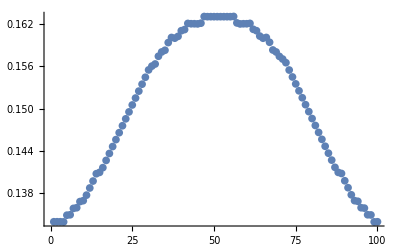

```mathematica
fileIndex=236;(*spot check one of the data files*)
indivplotfolder="/Users/chrisrichards/Desktop/FrogWork/CODE/mujoco150_KM/output/plots/z_old_23.7.2021";
SetDirectory[dataoutputfolder];
file=datafiles[[fileIndex]]
data=Import[file,"Data"];
ResetDirectory[];
ListPlot[data[[;;,1]]]
```

## Check plot grids (complicated)

Select a prefix for the conditions and select the corresponding figures and data

```mathematica
prefix="Figure_RUN_pro&ret";(*"Figure_HYP_axial", "Figure_HYP_pro&ret","Figure_RUN_axial", etc*)
matchFilesData={};
Do[
file=datafiles[[i]];
matchprefix=Quiet[StringTake[file,{1,StringLength[prefix]}]];
matchsuffix=StringTake[file,{StringLength[file]-3,StringLength[file]}];
If[
(matchprefix==prefix)(*&&(matchsuffix==".png")*),
matchFilesData=Join[matchFilesData,{file}]
];

,{i,1,Length[datafiles]}]
MatrixForm[Thread[{Range[Length[matchFilesData]],matchFilesData}]]

matchFilesPlot={};
Do[
file=plotfiles[[i]];
matchprefix=Quiet[StringTake[file,{1,StringLength[prefix]}]];
matchsuffix=StringTake[file,{StringLength[file]-3,StringLength[file]}];
If[
(matchprefix==prefix)&&(matchsuffix==".png"),
matchFilesPlot=Join[matchFilesPlot,{file}]
];

,{i,1,Length[plotfiles]}]
matchFilesPlot
SetDirectory[plotsfolder];
figs=Table[Import[matchFilesPlot[[i]]],{i,1,Length[matchFilesPlot]}];
ResetDirectory[];
Manipulate[figs[[i]],{i,1,Length[figs],1}]
```

(1 | Figure_RUN_pro&ret_LAL_hipL_KM02_RUN_02_AA.csv
2 | Figure_RUN_pro&ret_LAL_hipL_KM02_RUN_02_FE.csv
3 | Figure_RUN_pro&ret_LAL_hipL_KM02_RUN_02_fixed_AA.csv
4 | Figure_RUN_pro&ret_LAL_hipL_KM02_RUN_02_fixed_FE.csv
5 | Figure_RUN_pro&ret_LAL_hipL_KM02_RUN_02_fixed_LAR.csv
6 | Figure_RUN_pro&ret_LAL_hipL_KM02_RUN_02_LAR.csv
7 | Figure_RUN_pro&ret_LAMcrv_hipL_KM02_RUN_02_AA.csv
8 | Figure_RUN_pro&ret_LAMcrv_hipL_KM02_RUN_02_FE.csv
9 | Figure_RUN_pro&ret_LAMcrv_hipL_KM02_RUN_02_fixed_AA.csv
10 | Figure_RUN_pro&ret_LAMcrv_hipL_KM02_RUN_02_fixed_FE.csv
11 | Figure_RUN_pro&ret_LAMcrv_hipL_KM02_RUN_02_fixed_LAR.csv
12 | Figure_RUN_pro&ret_LAMcrv_hipL_KM02_RUN_02_LAR.csv
13 | Figure_RUN_pro&ret_LAMstr_hipL_KM02_RUN_02_AA.csv
14 | Figure_RUN_pro&ret_LAMstr_hipL_KM02_RUN_02_FE.csv
15 | Figure_RUN_pro&ret_LAMstr_hipL_KM02_RUN_02_fixed_AA.csv
16 | Figure_RUN_pro&ret_LAMstr_hipL_KM02_RUN_02_fixed_FE.csv
17 | Figure_RUN_pro&ret_LAMstr_hipL_KM02_RUN_02_fixed_LAR.csv
18 | Figure_RUN_pro&ret_LAMstr_hipL_KM02_RUN_02_LAR.csv
19 | Figure_RUN_pro&ret_LGR_hipL_KM02_RUN_02_AA.csv
20 | Figure_RUN_pro&ret_LGR_hipL_KM02_RUN_02_FE.csv
21 | Figure_RUN_pro&ret_LGR_hipL_KM02_RUN_02_fixed_AA.csv
22 | Figure_RUN_pro&ret_LGR_hipL_KM02_RUN_02_fixed_FE.csv
23 | Figure_RUN_pro&ret_LGR_hipL_KM02_RUN_02_fixed_LAR.csv
24 | Figure_RUN_pro&ret_LGR_hipL_KM02_RUN_02_LAR.csv
25 | Figure_RUN_pro&ret_LIEdist_hipL_KM02_RUN_02_AA.csv
26 | Figure_RUN_pro&ret_LIEdist_hipL_KM02_RUN_02_FE.csv
27 | Figure_RUN_pro&ret_LIEdist_hipL_KM02_RUN_02_fixed_AA.csv
28 | Figure_RUN_pro&ret_LIEdist_hipL_KM02_RUN_02_fixed_FE.csv
29 | Figure_RUN_pro&ret_LIEdist_hipL_KM02_RUN_02_fixed_LAR.csv
30 | Figure_RUN_pro&ret_LIEdist_hipL_KM02_RUN_02_LAR.csv
31 | Figure_RUN_pro&ret_LIEprox_hipL_KM02_RUN_02_AA.csv
32 | Figure_RUN_pro&ret_LIEprox_hipL_KM02_RUN_02_FE.csv
33 | Figure_RUN_pro&ret_LIEprox_hipL_KM02_RUN_02_fixed_AA.csv
34 | Figure_RUN_pro&ret_LIEprox_hipL_KM02_RUN_02_fixed_FE.csv
35 | Figure_RUN_pro&ret_LIEprox_hipL_KM02_RUN_02_fixed_LAR.csv
36 | Figure_RUN_pro&ret_LIEprox_hipL_KM02_RUN_02_LAR.csv
37 | Figure_RUN_pro&ret_LIFB_hipL_KM02_RUN_02_AA.csv
38 | Figure_RUN_pro&ret_LIFB_hipL_KM02_RUN_02_FE.csv
39 | Figure_RUN_pro&ret_LIFB_hipL_KM02_RUN_02_fixed_AA.csv
40 | Figure_RUN_pro&ret_LIFB_hipL_KM02_RUN_02_fixed_FE.csv
41 | Figure_RUN_pro&ret_LIFB_hipL_KM02_RUN_02_fixed_LAR.csv
42 | Figure_RUN_pro&ret_LIFB_hipL_KM02_RUN_02_LAR.csv
43 | Figure_RUN_pro&ret_LIFM_hipL_KM02_RUN_02_AA.csv
44 | Figure_RUN_pro&ret_LIFM_hipL_KM02_RUN_02_FE.csv
45 | Figure_RUN_pro&ret_LIFM_hipL_KM02_RUN_02_fixed_AA.csv
46 | Figure_RUN_pro&ret_LIFM_hipL_KM02_RUN_02_fixed_FE.csv
47 | Figure_RUN_pro&ret_LIFM_hipL_KM02_RUN_02_fixed_LAR.csv
48 | Figure_RUN_pro&ret_LIFM_hipL_KM02_RUN_02_LAR.csv
49 | Figure_RUN_pro&ret_LIIlat_hipL_KM02_RUN_02_AA.csv
50 | Figure_RUN_pro&ret_LIIlat_hipL_KM02_RUN_02_FE.csv
51 | Figure_RUN_pro&ret_LIIlat_hipL_KM02_RUN_02_fixed_AA.csv
52 | Figure_RUN_pro&ret_LIIlat_hipL_KM02_RUN_02_fixed_FE.csv
53 | Figure_RUN_pro&ret_LIIlat_hipL_KM02_RUN_02_fixed_LAR.csv
54 | Figure_RUN_pro&ret_LIIlat_hipL_KM02_RUN_02_LAR.csv
55 | Figure_RUN_pro&ret_LIImed_hipL_KM02_RUN_02_AA.csv
56 | Figure_RUN_pro&ret_LIImed_hipL_KM02_RUN_02_FE.csv
57 | Figure_RUN_pro&ret_LIImed_hipL_KM02_RUN_02_fixed_AA.csv
58 | Figure_RUN_pro&ret_LIImed_hipL_KM02_RUN_02_fixed_FE.csv
59 | Figure_RUN_pro&ret_LIImed_hipL_KM02_RUN_02_fixed_LAR.csv
60 | Figure_RUN_pro&ret_LIImed_hipL_KM02_RUN_02_LAR.csv
61 | Figure_RUN_pro&ret_LOE_hipL_KM02_RUN_02_AA.csv
62 | Figure_RUN_pro&ret_LOE_hipL_KM02_RUN_02_FE.csv
63 | Figure_RUN_pro&ret_LOE_hipL_KM02_RUN_02_fixed_AA.csv
64 | Figure_RUN_pro&ret_LOE_hipL_KM02_RUN_02_fixed_FE.csv
65 | Figure_RUN_pro&ret_LOE_hipL_KM02_RUN_02_fixed_LAR.csv
66 | Figure_RUN_pro&ret_LOE_hipL_KM02_RUN_02_LAR.csv
67 | Figure_RUN_pro&ret_LSA_hipL_KM02_RUN_02_AA.csv
68 | Figure_RUN_pro&ret_LSA_hipL_KM02_RUN_02_FE.csv
69 | Figure_RUN_pro&ret_LSA_hipL_KM02_RUN_02_fixed_AA.csv
70 | Figure_RUN_pro&ret_LSA_hipL_KM02_RUN_02_fixed_FE.csv
71 | Figure_RUN_pro&ret_LSA_hipL_KM02_RUN_02_fixed_LAR.csv
72 | Figure_RUN_pro&ret_LSA_hipL_KM02_RUN_02_LAR.csv
73 | Figure_RUN_pro&ret_LSM_hipL_KM02_RUN_02_AA.csv
74 | Figure_RUN_pro&ret_LSM_hipL_KM02_RUN_02_FE.csv
75 | Figure_RUN_pro&ret_LSM_hipL_KM02_RUN_02_fixed_AA.csv
76 | Figure_RUN_pro&ret_LSM_hipL_KM02_RUN_02_fixed_FE.csv
77 | Figure_RUN_pro&ret_LSM_hipL_KM02_RUN_02_fixed_LAR.csv
78 | Figure_RUN_pro&ret_LSM_hipL_KM02_RUN_02_LAR.csv)

{Figure_RUN_pro&ret_AA_relativeScaling.png,Figure_RUN_pro&ret_FE_relativeScaling.png,Figure_RUN_pro&ret_LAR_relativeScaling.png}

Select from matchFilesData which one you want to check.

Figure_RUN_pro&ret_LSM_hipL_KM02_RUN_02_FE.csv

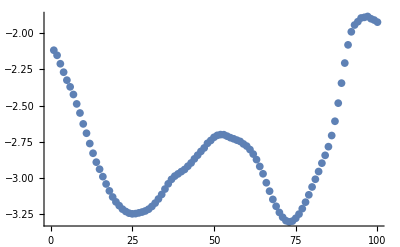

```mathematica
file=matchFilesData[[74]]
SetDirectory[dataoutputfolder];
data=Import[file,"Data"];
ResetDirectory[];
ListPlot[data[[;;,1]]]
```